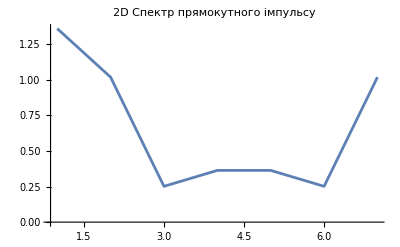

```mathematica
(*Прямокутний імпульс-Варіант 13*)
(*Встановлюємо параметри для прямокутного імпульсу*)
A1=1.2;τ1=5*10^-3;analysisInterval1=3*τ1;
(*Визначаємо функцію прямокутного імпульсу*)
rectImpulse[t_]:=A1*Boole[0<=t<=τ1];
(*Частота дискретизації за теоремою Найквіста*)
fs1=2/τ1;
Ts1=1/fs1;
nMax1=Floor[analysisInterval1/Ts1];
(*Отримуємо дискретний сигнал*)
discreteSignal1=Table[rectImpulse[n Ts1],{n,0,nMax1}];
(*Здійснюємо дискретне перетворення Фур’є*)
DFT1=Fourier[discreteSignal1];

(*Візуалізація 3D спектру*)
GraphicsRow[{ListPlot3D[Table[{n,Abs[DFT1[[n]]],Im[DFT1[[n]]]},{n,1,Length[DFT1]}],Mesh->None,PlotRange->All,PlotLabel->"3D Спектр прямокутного імпульсу",ColorFunction->"Rainbow",PlotStyle->Directive[Opacity[0.7]]],

(*Лінійний графік у 2D*)
ListLinePlot[Abs[DFT1],PlotRange->All,PlotLabel->"2D Спектр прямокутного імпульсу"]}]
```

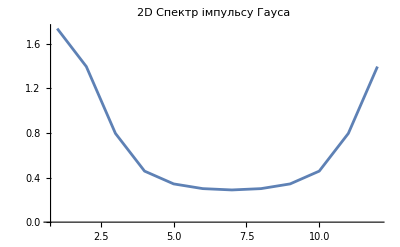

```mathematica
(*Імпульс Гауса-Варіант 14*)
(*Встановлюємо параметри для імпульсу Гауса*)
A2=2;τ2=4.5*10^-3;TC=25*10^-3;
(*Визначаємо функцію Гаусового імпульсу*)
gaussianImpulse[t_]:=A2*Exp[-(t^2)/(2*τ2^2)];
(*Частота дискретизації*)
fs2=2/τ2;
Ts2=1/fs2;
nMax2=Floor[TC/Ts2];
(*Отримуємо дискретний сигнал*)
discreteSignal2=Table[gaussianImpulse[n Ts2],{n,0,nMax2}];
(*Здійснюємо дискретне перетворення Фур’є*)
DFT2=Fourier[discreteSignal2];

(*Візуалізація 3D спектру*)
GraphicsRow[{ListPlot3D[Table[{n,Abs[DFT2[[n]]],Im[DFT2[[n]]]},{n,1,Length[DFT2]}],Mesh->None,PlotRange->All,PlotLabel->"3D Спектр імпульсу Гауса",ColorFunction->"SunsetColors",PlotStyle->Directive[Opacity[0.7]]],

(*Лінійний графік у 2D*)
ListLinePlot[Abs[DFT2],PlotRange->All,PlotLabel->"2D Спектр імпульсу Гауса"]}]
```

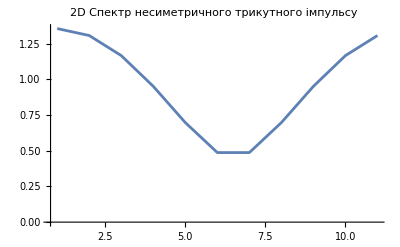

```mathematica
(*Несиметричний трикутний імпульс-Варіант 15*)
(*Встановлюємо параметри для несиметричного трикутного імпульсу*)
A3=3;τ3=5*10^-3;analysisInterval3=25*10^-3;
(*Визначаємо функцію несиметричного трикутного імпульсу*)
asymTriImpulse[t_]:=Piecewise[{{(A3*t)/τ3,0<=t<=τ3}},0];
(*Частота дискретизації*)
fs3=2/τ3;
Ts3=1/fs3;
nMax3=Floor[analysisInterval3/Ts3];
(*Отримуємо дискретний сигнал*)
discreteSignal3=Table[asymTriImpulse[n Ts3],{n,0,nMax3}];
(*Здійснюємо дискретне перетворення Фур’є*)
DFT3=Fourier[discreteSignal3];

(*Візуалізація 3D спектру*)
GraphicsRow[{ListPlot3D[Table[{n,Abs[DFT3[[n]]],Im[DFT3[[n]]]},{n,1,Length[DFT3]}],Mesh->None,PlotRange->All,PlotLabel->"3D Спектр несиметричного трикутного імпульсу",ColorFunction->"TemperatureMap",PlotStyle->Directive[Opacity[0.7]]],

(*Лінійний графік у 2D*)
ListLinePlot[Abs[DFT3],PlotRange->All,PlotLabel->"2D Спектр несиметричного трикутного імпульсу"]}]
```

```mathematica
(*Симетричний трикутний імпульс-Варіант 16*)
(*Встановлюємо параметри для симетричного трикутного імпульсу*)
A4=3;τ4=7*10^-3;analysisInterval4=25*10^-3;
(*Визначаємо функцію симетричного трикутного імпульсу*)
symTriImpulse[t_]:=Piecewise[{{A4*(1-Abs[t-τ4]/τ4),0<=t<=2*τ4}},0];
(*Частота дискретизації*)
fs4=2/τ4;
Ts4=1/fs4;
nMax4=Floor[analysisInterval4/Ts4];
(*Отримуємо дискретний сигнал*)
discreteSignal4=Table[symTriImpulse[n Ts4],{n,0,nMax4}];
(*Здійснюємо дискретне перетворення Фур’є*)
DFT4=Fourier[discreteSignal4];

(*Візуалізація 3D спектру*)
GraphicsRow[{ListPlot3D[Table[{n,Abs[DFT4[[n]]],Im[DFT4[[n]]]},{n,1,Length[DFT4]}],Mesh->None,PlotRange->All,PlotLabel->"3D Спектр симетричного трикутного імпульсу",ColorFunction->"NeonColors",PlotStyle->Directive[Opacity[0.7]]],

(*Лінійний графік у 2D*)
ListLinePlot[Abs[DFT4],PlotRange->All,PlotLabel->"2D Спектр симетричного трикутного імпульсу"]}]
```

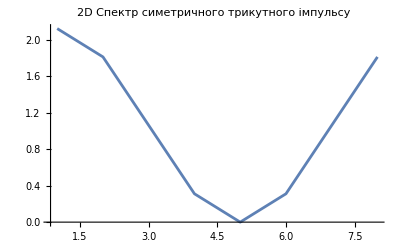

```mathematica
(* ===Параметри та початкові налаштування симетричний трикутний імпульс (варіант 8)===*)
(*Параметри сигналу*)
A=2; (*Амплітуда*)
tau=3*10^-3; (*Тривалість імпульсу в секундах*)
tMax=15*10^-3; (*Тривалість сигналу в секундах*)
numSamples=128; (*Кількість відліків*)

(*Частота дискретизації*)
fs=numSamples/tMax; (*Частота дискретизації*)
Ts=1/fs; (*Період дискретизації*)

(* ===1.3.1:Дискретизація неперервного сигналу===*)
(*Функція неперервного симетричного трикутного імпульсу*)
continuousSignal[t_]:=A*(1-Abs[(t-tau/2)/tau])

(*Масив часу для неперервного сигналу*)
tContinuous=Range[0,tMax,tMax/1000];
continuousValues=continuousSignal/@tContinuous;

(*Дискретизація сигналу*)
tDiscrete=Range[0,tMax,Ts];
discreteValues=continuousSignal/@tDiscrete;

(* ===Построєння графіків неперервного та дискретного сигналів===*)
continuousPlot=ListLinePlot[Transpose[{tContinuous,continuousValues}],PlotStyle->Blue,PlotLegends->{"Неперервний сигнал"}];
discretePlot=ListPlot[Transpose[{tDiscrete,discreteValues}],PlotStyle->{Red,PointSize[0.015]},PlotLegends->{"Дискретний сигнал"}];

(* ===1.3.2:Амплітудний спектр неперервного сигналу===*)
(*Спектр частот 0... fs для неперервного сигналу*)
continuousSpectrumFreqs=Range[0,fs,fs/Length[continuousValues]];
continuousSpectrum=Abs[Fourier[continuousValues]];

(* ===1.3.3:Амплітудний спектр дискретного сигналу===*)
(*Використання дискретного перетворення Фур'є*)
discreteSpectrum=Abs[Fourier[discreteValues]];

(* ===1.3.4:Алгоритм ДПФ для дискретного сигналу===*)
(*Періодичне повторення масиву ДПФ для побудови повного спектра*)
DFTAlgorithm[s_]:=Module[{N=Length[s]},Table[Sum[s[[k+1]]*Exp[-2 Pi I (k-1) (n-1)/N],{k,0,N-1}],{n,0,N-1}]];
customDFT=Abs[DFTAlgorithm[discreteValues]];

(* ===1.3.5:Амплітудний спектр з використанням команди fft===*)
fftSpectrum=Abs[Fourier[discreteValues]];

(* ===1.3.6:Порівняння спектрів неперервного та дискретного сигналів===*)
(*Побудова всіх спектрів на одному графічному полі для порівняння*)
spectrumPlot=ListLinePlot[{Table[{n,continuousSpectrum[[n]]},{n,1,Length[continuousSpectrum]}],Table[{n,discreteSpectrum[[n]]},{n,1,Length[discreteSpectrum]}],Table[{n,customDFT[[n]]},{n,1,Length[customDFT]}],Table[{n,fftSpectrum[[n]]},{n,1,Length[fftSpectrum]}]},PlotLegends->{"Неперервний спектр","Дискретний спектр","Спектр ДПФ","Спектр ДПФ (FFT)"},PlotRange->All,PlotStyle->{Blue,Red,Green,Purple}];

(* ===Відображення всіх графіків разом===*)
GraphicsGrid[{{Show[continuousPlot,discretePlot,PlotLabel->"Неперервний та дискретний сигнали"]},{Show[spectrumPlot,PlotLabel->"Порівняння спектрів неперервного та дискретного сигналів"]}}]

(* ===Построєння 3D графіків неперервного та дискретного сигналів===*)
continuousPlot3D=ListPlot3D[Table[{tContinuous[[n]],continuousValues[[n]],0},{n,Length[tContinuous]}],Mesh->None,PlotRange->All,PlotLabel->"3D графік неперервного сигналу",ColorFunction->"Rainbow",PlotStyle->Directive[Opacity[0.7]],AxesLabel->{"Час","Амплітуда","Z"}];

discretePlot3D=ListPointPlot3D[Table[{tDiscrete[[n]],discreteValues[[n]],0},{n,Length[tDiscrete]}],PlotRange->All,PlotLabel->"3D графік дискретного сигналу",ColorFunction->"Rainbow",PlotStyle->Directive[PointSize[Medium],Red],AxesLabel->{"Час","Амплітуда","Z"}];

(* ===1.3.2:Амплітудний спектр неперервного сигналу===*)
continuousSpectrumFreqs=Range[0,fs,fs/Length[continuousValues]];
continuousSpectrum=Abs[Fourier[continuousValues]];

(*3D графік амплітудного спектру неперервного сигналу*)
continuousSpectrum3D=ListPlot3D[Table[{continuousSpectrumFreqs[[n]],continuousSpectrum[[n]],0},{n,Length[continuousSpectrum]}],Mesh->None,PlotRange->All,PlotLabel->"3D Спектр неперервного сигналу",ColorFunction->"TemperatureMap",AxesLabel->{"Частота","Амплітуда","Z"}];

(* ===1.3.3:Амплітудний спектр дискретного сигналу===*)
discreteSpectrum=Abs[Fourier[discreteValues]];

(*3D графік амплітудного спектру дискретного сигналу*)
discreteSpectrum3D=ListPlot3D[Table[{n,discreteSpectrum[[n]],0},{n,Length[discreteSpectrum]}],Mesh->None,PlotRange->All,PlotLabel->"3D Спектр дискретного сигналу",ColorFunction->"SunsetColors",AxesLabel->{"Частота","Амплітуда","Z"}];

(* ===1.3.4:Алгоритм ДПФ для дискретного сигналу===*)
DFTAlgorithm[s_]:=Module[{N=Length[s]},Table[Sum[s[[k+1]]*Exp[-2 Pi I (k-1) (n-1)/N],{k,0,N-1}],{n,0,N-1}]];
customDFT=Abs[DFTAlgorithm[discreteValues]];

(*3D графік амплітудного спектру ДПФ*)
customDFT3D=ListPlot3D[Table[{n,customDFT[[n]],0},{n,Length[customDFT]}],Mesh->None,PlotRange->All,PlotLabel->"3D Спектр ДПФ",ColorFunction->"NeonColors",AxesLabel->{"Частота","Амплітуда","Z"}];

(* ===1.3.5:Амплітудний спектр з використанням команди fft===*)
fftSpectrum=Abs[Fourier[discreteValues]];

(*3D графік амплітудного спектру FFT*)
fftSpectrum3D=ListPlot3D[Table[{n,fftSpectrum[[n]],0},{n,Length[fftSpectrum]}],Mesh->None,PlotRange->All,PlotLabel->"3D Спектр FFT",ColorFunction->"NeonColors",AxesLabel->{"Частота","Амплітуда","Z"}];

(* ===Відображення всіх графіків разом===*)
GraphicsRow[{Show[continuousPlot3D,PlotLabel->"Неперервний сигнал"],Show[discretePlot3D,PlotLabel->"Дискретний сигнал"]}]

GraphicsRow[{Show[continuousSpectrum3D,PlotLabel->"Спектр неперервного сигналу"],Show[discreteSpectrum3D,PlotLabel->"Спектр дискретного сигналу"],Show[customDFT3D,PlotLabel->"Спектр ДПФ"],Show[fftSpectrum3D,PlotLabel->"Спектр FFT"]}]
```

-Graphics-

-Graphics-

-Graphics-

Висновки до лабораторної роботи

У цій лабораторній роботі були досліджені різні види імпульсів — прямокутний, Гауса несиметричний трикутний і симетричний трикутний імпульси. 
Основними кроками роботи стали дискретизація, проведення дискретного перетворення Фур’є (ДПФ) для аналізу частотного спектру кожного імпульсу, а також візуалізація 2D та 3D спектрів.

1) Дискретизація імпульсів: виконано дискретизацію для всіх типів імпульсів, де частоти дискретизації були вибрані відповідно до теореми Найквіста, щоб уникнути накладання спектрів (аліасингу) і зберегти основні частотні компоненти імпульсу.

2) Перетворення Фур’є: було проведено ДПФ для кожного імпульсу, що дозволило визначити спектральні компоненти і виявити залежність спектра від форми імпульсу. Зокрема:
Прямокутний імпульс має розподіл частот у вигляді синусоїдального спектру з основною частотою, що обумовлена тривалістю імпульсу.
Гаусів імпульс дає спектр з плавним спадом, що відповідає експоненціальному характеру його форми.
Трикутні імпульси мають спектри, схожі до спектрів прямокутного імпульсу, проте їхній спад у частотній області більш плавний завдяки лінійному збільшенню та зменшенню амплітуди.

3) Візуалізація спектрів: побудова 2D та 3D спектрів дозволила оцінити основні частотні компоненти та їх амплітуди. Результати показали, що:
Прямокутний і несиметричний трикутний імпульси мають яскраво виражені гармонічні складові.
Гаусів імпульс має більш рівномірний спектр, оскільки він характеризується плавним експоненційним спадом.
Симетричний трикутний імпульс має спектр, схожий на прямокутний, але зі зменшеними гармоніками, що відображає його більш плавний профіль у часовій області.

4) Порівняння результатів ДПФ та FFT: було продемонстровано, що результати, отримані за допомогою власної реалізації алгоритму ДПФ, співпадають із результатами вбудованої функції fft, підтверджуючи точність реалізації ДПФ.

5) Аналіз спектрів неперервних та дискретних сигналів: порівняння спектрів показало важливість вибору правильної частоти дискретизації для отримання адекватного представлення спектра оригінального сигналу.

Загалом, проведений аналіз показав, що форма імпульсу має значний вплив на його спектральний склад. Завдяки спектральному аналізу стало можливим зрозуміти, як різні імпульси ведуть себе у частотній області, що є важливим для проектування та використання цифрових фільтрів у задачах обробки сигналів.